# Exercise 1.2

## Band structure of the disordered SSH model with nearest-neighbours interactions and OBC.

The following cell evaluates a random symmetric tridiagonal matrix representing the Hamiltonian of a disordered SSH model with only nearest neighbours coupling. The disorder is a random number between -R and R, so we simply compute a random number between -1 and 1 and plot E/R. The system has open boundary conditions (OBC).

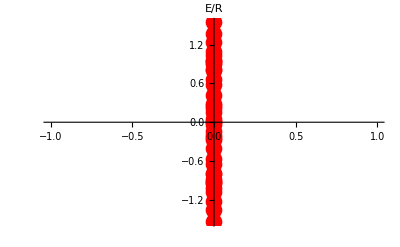

```mathematica
ClearAll;
n=20;
mat=SparseArray[
Table[
{i,i+1}->RandomReal[{-1,1}],
{i,1,2n-1}
],
{2n,2n},0.];
H=mat+Transpose[mat];
energy=Eigenvalues[H];
ListPlot[Table[{0,energy[[i]]},{i,1,2n}],
PlotStyle->{Red,PointSize[.03]},Ticks->{None,Automatic},AxesStyle->Directive[Black, 12],AxesLabel->{None,"E/R"}]
```

Now we compute the splitting between the “edge states” as a function of the number of unit cells (again with OBC).

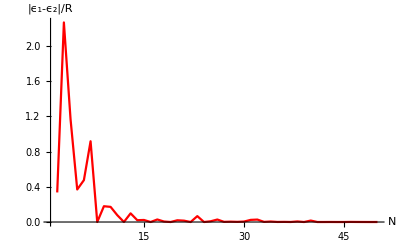

```mathematica
ClearAll;
list={};
For[k=2,k≤ 50,k+=1,
mat=SparseArray[
Table[
{i,i+1}->RandomReal[{-1,1}],
{i,1,2k-1}
],
{2k,2k},0.];
H=mat+Transpose[mat];
{e1,e2}=Eigenvalues[H,-2];
AppendTo[list,{k,2*Abs[e1-e2]}];
]
ListPlot[list,PlotStyle->{Red,PointSize[.015]},AxesLabel->{"N","|ϵ_1-ϵ_2|/R"},AxesStyle->Directive[Black, 12],PlotRange->All,Joined->True]
```

## Band structure of the disordered SSH model with nearest-neighbours interactions and PBC.

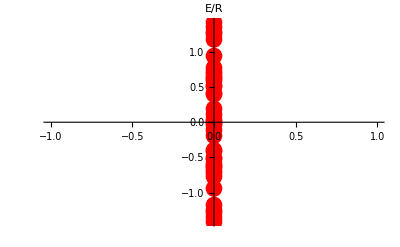

```mathematica
n=20;
mat=SparseArray[Append[
Table[
{i,i+1}->RandomReal[{-1,1}],
{i,1,2n-1}
],
{1,2n}->RandomReal[{-1,1}]
],
{2n,2n},0.];
H=mat+Transpose[mat];
energy=Eigenvalues[H];
ListPlot[Table[{0,energy[[i]]},{i,1,2n}],
PlotStyle->{Red,PointSize[.03]},Ticks->{None,Automatic},AxesStyle->Directive[Black, 12],AxesLabel->{None,"E/R"}]
```

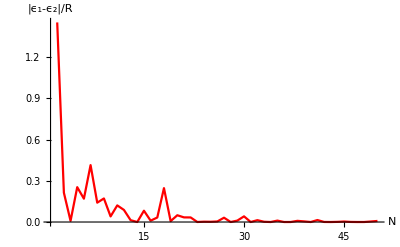

```mathematica
ClearAll;
list={};
For[k=2,k≤ 50,k+=1,
mat=SparseArray[
Table[
{i,i+1}->RandomReal[{-1,1}],
{i,1,2k-1}
],
{2k,2k},0.];
H=mat+Transpose[mat];
{e1,e2}=Eigenvalues[H,-2];
AppendTo[list,{k,2*Abs[e1-e2]}];
]
ListPlot[list,PlotStyle->{Red,PointSize[.015]},AxesLabel->{"N","|ϵ_1-ϵ_2|/R"},AxesStyle->Directive[Black, 12],PlotRange->All,Joined->True]
```